Vojtěch Myslivec, FIT ČVUT v Praze, 2015/2016

# Kryptosystém McEliece

## McEliece – Implementace

### Chybove zpravy

```mathematica
McEliece::delkam="Zpráva m musí být délky k";
McEliece::delkac="Zpráva c musí být délky n";
```

### nahodnaPermutacniMatice

Náhodná permutační matice n×n

```mathematica
Unprotect[nahodnaPermutacniMatice];
ClearAll[nahodnaPermutacniMatice];
```

```mathematica
nahodnaPermutacniMatice[n_]:=RandomSample[IdentityMatrix[n]]
```

```mathematica
Protect[nahodnaPermutacniMatice];
```

### nahodnaRegularniMatice

Náhodná regulární matice k×k (nad ℤ_2)
Vraci matici M a pocet pokusu, kolik matic bylo treba vygenerovat.

```mathematica
Unprotect[nahodnaRegularniMatice];
ClearAll[nahodnaRegularniMatice];
```

```mathematica
nahodnaRegularniMatice[k_]:=Module[
{r=0,M,i=0},
While[
r≠k,
M=RandomChoice[{0,1},{k,k}];
r=MatrixRank[M,Modulus->2];
i++
];
{M,i}
]
```

```mathematica
Protect[nahodnaRegularniMatice];
```

### generujMcEliece

Lineární kód (n,k) opravující t chyb,
 - generujici matice G
 - náhodná k×k regulární matice S
 - náhodná n×n permutační matice P

Parametry (n, k, t), veřejný klíč (OverHat[G)], soukromý klíč (G, S^-1, P^-1)

```mathematica
Unprotect[generujMcEliece];
ClearAll[generujMcEliece];
```

```mathematica
generujMcEliece[
m_Integer/;m≥ 2,
t_Integer/;t≥2,
verbose_Symbol:False
]/;BooleanQ[verbose]:=Module[{
p=2,n,k,
GoppaKod,matG,matS,matP,hatG,
soukromyKlic,verejnyKlic,parametry
},
n=p^m;k=n-m t;

GoppaKod=generujBinarniGoppaKod[m,t];
matG=GoppaKod⟦1⟧;
matS=nahodnaRegularniMatice[k]⟦1⟧;
matP=nahodnaPermutacniMatice[n];
hatG=dotNad2[matS,matG,matP];

If[verbose==True,
Print[
"Ĝ = SGP = ",matS//MatrixForm,matG//MatrixForm,matP//MatrixForm ,
"\nĜ =",hatG//MatrixForm
];
];

parametry={n,k,t};
verejnyKlic={hatG};
soukromyKlic={GoppaKod,Inverse[matS,Modulus->2],Inverse[matP,Modulus->2]};

{soukromyKlic,verejnyKlic,parametry}
]
```

```mathematica
Protect[generujMcEliece];
```

### sifrujMcEliece

Algoritmus: “zakódovat” zprávu m (délky k), pomocí “generující” matice Ĝ a přičíst náhodný chybový vektor z (délky n) s Hammingovou vahou max. t
c=m Ĝ+z

```mathematica
Unprotect[sifrujMcEliece];
ClearAll[sifrujMcEliece];
sifrujMcEliece::delkam=McEliece::delkam;
```

```mathematica
sifrujMcEliece[
m_List,
verejnyKlic:{hatG_List},
parametry:{n_Integer,k_Integer,t_Integer}
]:=Module[{
p=2,c,
z=nahodnyChybovyVektor[n,t]
},
If[Length[m]≠k,
Print[sifrujMcEliece::delkam];
Return[]
];
c=plus[dotNad2[m,hatG],z,p];
c
]
```

```mathematica
Protect[sifrujMcEliece];
```

### desifrujMcEliece

Algoritmus:
 - získat ĉ=c P^-1 – inverze permutace
 - dekódovat m̂ z ĉ – kód odstraní chybový vektor
 - vypočítat původní zprávu m=m̂ S^-1

```mathematica
Unprotect[desifrujMcEliece];
ClearAll[desifrujMcEliece];
desifrujMcEliece::delkac=McEliece::delkac;
```

```mathematica
desifrujMcEliece[
c_List,
soukromyKlic:{GoppaKod_List,invS_List,invP_List},
parametry:{n_Integer,k_Integer,t_Integer}
]:=Module[{
hatc,hatm,m
},
If[Length[c]≠n,
Print[desifrujMcEliece::delkac];
Return[]
];
hatc=dotNad2[c,invP];
hatm=dekodujBinarniGoppaKod[hatc,GoppaKod]⟦1⟧;
m=dotNad2[hatm,invS];
m
]
```

```mathematica
Protect[desifrujMcEliece];
```

## McEliece – Příklad použití

### Generování klíčů

```mathematica
m=4;
t=3;
{soukromyKlic,verejnyKlic,parametry}=generujMcEliece[m,t,True];
```

### Šifrováni

```mathematica
zprava=nahodnyPolynom[2,parametry⟦2⟧]
c=sifrujMcEliece[zprava,verejnyKlic,parametry]
```

### Dešifrováni

```mathematica
m=desifrujMcEliece[c,soukromyKlic,parametry]
m==zprava
```

## Časové složitosti

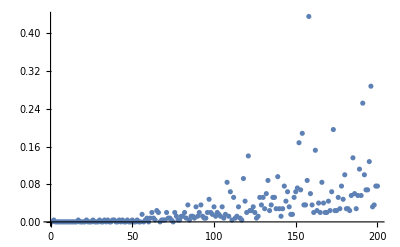

```mathematica
cas={#,Timing[nahodnaRegularniMatice[#]]⟦1⟧}&/@Range[200];
ListPlot[cas,PlotRange->All]
```